# Изпит

## Задача 1: Дадено е уравнението

```mathematica
f[x_]:= x^2-30Sin[x+π/(5+1)]-(5+8)
```

```mathematica
f[x]
```

{87+30 Sin[10-π/6],-28,87-30 Sin[10+π/6]}

### a) Да се намери общия брой на корените на уравнението

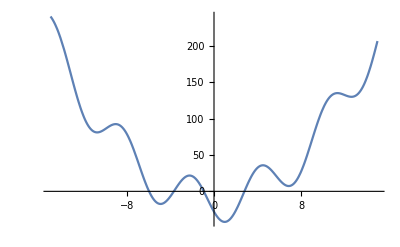

```mathematica
Plot[f[x],{x,-15,15}]
```

Извод: Функцията има 4 корена

### б) Да се локализира най-големия корен в интервал [p,q]

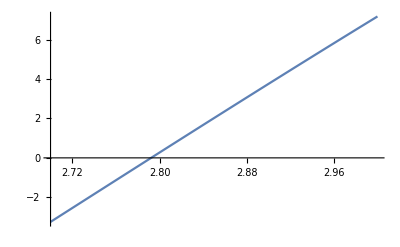

```mathematica
Plot[f[x],{x,2.7,3}]
```

```mathematica
f[2.7]
```

-3.25257

```mathematica
f[3]//N
```

7.18348

Извод: Функцията е непрекъсната и има различни знаци в двата края на разглеждания интервал [2.7 ; 3].
Следователно има поне един корен в разглеждания интервал [2.7 ; 3].

### в) Да се проверят условията за приложение на метода на допирателните (Нютон)

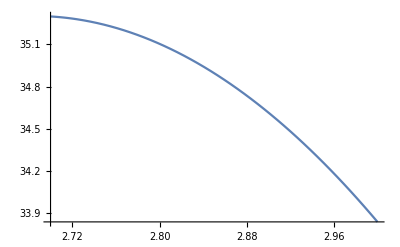

```mathematica
Plot[f'[x],{x,2.7,3}]
```

Извод: Първата производна има само положителни стойности в целия раглеждан интервал [2.7 ; 3].

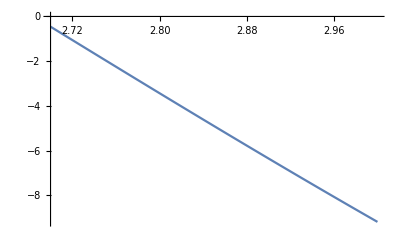

```mathematica
Plot[f''[x],{x,2.7,3}]
```

Извод: Втората производна има само отрицателни стойности в целия раглеждан интервал [2.7 ; 3].

### г) Да се определи началното приближение за итерационния процес по метода на Нютон

x0 = ?, такова че f (x0).f’’(x) > 0

```mathematica
f[2.7]
```

-3.25257

```mathematica
f[3]//N
```

7.18348

```mathematica
x0 = 2.7
```

2.7

### д) Да се изчисли корена по метода на допирателните (Нютон) с точност 10^-4. Представете таблицата с изчисленията.

Определяне на постоянните величини

M2 = max[a,b]|f’’(x)|

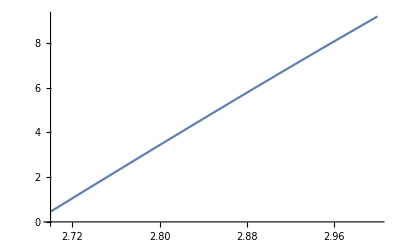

```mathematica
Plot[Abs[f''[x]],{x,2.7,3}]
```

```mathematica
M2=Abs[f''[3]]//N
```

9.18348

m1 = min[a,b]|f’(x)|

```mathematica
Plot[Abs[f'[x]],{x,2.7,3}]
```

-Graphics-

```mathematica
m1=Abs[f'[3]]//N
```

33.8376

```mathematica
P=M2/(2m1)
```

0.1357

Извършване на итерациите

```mathematica
p=5;q=8;
f[x_]:= x^2-30Sin[x+π/(5+1)]-(5+8)
x0 = 2.7;
M2=Abs[f''[3]];
m1=Abs[f'[3]];
P=M2/(2m1);

Print["n = ", 0, " x_n = ", x0, " f(x_n) = ",f[x0], " f'(x_n) = ",f'[x0]]
epszad = 10^-4;
eps = 1;
For[n=1,eps>epszad,n++,
x1=x0-f[x0]/f'[x0];
eps = P * Abs[x1-x0]^2;
x0=x1;
Print["n = ",n," x_n = ",x0,
" f(x_n) = ",f[x0]," f'(x_n) = ",f'[x0]," ε_n = ",eps]
]
```

n = 0 x_n = 2.7 f(x_n) = -3.25257 f'(x_n) = 35.2992

n = 1 x_n = 2.79214 f(x_n) = -0.0058313 f'(x_n) = 35.1305 ε_n = 0.00115213

n = 2 x_n = 2.79231 f(x_n) = -4.40805×10^-8 f'(x_n) = 35.13 ε_n = 3.73887×10^-9

### е) Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал за същата точност.

```mathematica
Log[(3-2.7)/10^-4]-1
```

7.00637

### ж) Да се направи сравнение кой метод е по ефективен за избрания интервал.

Извод: По метода на раполовяването биха били необходими 8 итерации за достигане на
исканата точност. А по метода на допирателните бяха достатъчни 2 итерации. Следователно
методът на допирателните е по-ефективен.

## Задача 3:

### a)

Да се състави таблицата (x_i , f(x_i)), където
	x_i = −a + i(0.5), i = -5, 5 , f(x) = x-(8+1)sin x.

Генериране на х

```mathematica
xt= Table[5+i*0.5,{i,-5,5}]
```

{2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5}

Генериране на у

```mathematica
f[x_]:= x-(8+1)Sin[x]
```

```mathematica
yt = f[xt]
```

{-2.88625,1.72992,6.65705,10.8112,13.2978,13.6303,11.8499,8.51474,4.56392,1.08712,-0.942}

Графика на функцията

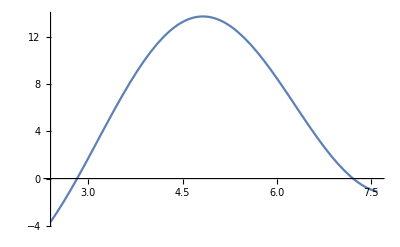

```mathematica
grf=Plot[f[x],{x,2.4,7.6}]
```

```mathematica
n=Length[xt]
```

11

```mathematica
points = Table[{xt[[i]], yt[[i]]},{i,1,n}]
```

{{2.5,-2.88625},{3.,1.72992},{3.5,6.65705},{4.,10.8112},{4.5,13.2978},{5.,13.6303},{5.5,11.8499},{6.,8.51474},{6.5,4.56392},{7.,1.08712},{7.5,-0.942}}

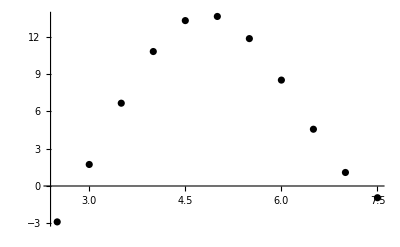

```mathematica
grp = ListPlot[points,PlotStyle->Black]
```

### б) Изберете 4 подходящи точки, по които да се построи интерполационен полином за изчисляването на приближената стойност на функцията в точката

```mathematica
z= 5+(-1)^8(0.23)8+0.01
```

6.85

```mathematica
tableOfPoints = Prepend[points,{"X_i","Y_i"}]
tableOfPoints2=MapThread[Prepend,{tableOfPoints,{"",1,2,3,4,5,6,7,8,9,10,11}}]
Grid[tableOfPoints2,Frame->All]
```

{{X_i,Y_i},{2.5,-2.88625},{3.,1.72992},{3.5,6.65705},{4.,10.8112},{4.5,13.2978},{5.,13.6303},{5.5,11.8499},{6.,8.51474},{6.5,4.56392},{7.,1.08712},{7.5,-0.942}}

{{,X_i,Y_i},{1,2.5,-2.88625},{2,3.,1.72992},{3,3.5,6.65705},{4,4.,10.8112},{5,4.5,13.2978},{6,5.,13.6303},{7,5.5,11.8499},{8,6.,8.51474},{9,6.5,4.56392},{10,7.,1.08712},{11,7.5,-0.942}}

| X_i | Y_i
1 | 2.5 | -2.88625
2 | 3. | 1.72992
3 | 3.5 | 6.65705
4 | 4. | 10.8112
5 | 4.5 | 13.2978
6 | 5. | 13.6303
7 | 5.5 | 11.8499
8 | 6. | 8.51474
9 | 6.5 | 4.56392
10 | 7. | 1.08712
11 | 7.5 | -0.942

Четирите подходящи точки които избирам са  8,9,10,11

### в) Конструирайте полинома по избраните точки

```mathematica
L3[x_]:= 8.51474*((x-(6.5))(x-(7))(x-(7.5)))/((6-(6.5))(6-(7))(6-(7.5)))+ 4.56392*((x-(6))(x-(7))(x-(7.5)))/((6.5-(6))(6.5-(7))(6.5-(7.5)))+1.08712*((x-(6))(x-(6.5))(x-(7.5)))/((7-(6))(7-(6.5))(7-(7.5)))+-0.942*((x-(6))(x-(6.5))(x-(7)))/((7.5-(6))(7.5-(6.5))(7.5-(7)))
```

```mathematica
Expand[L3[x]]
```

{-5441.16,-261.514,44.7057}

### г) Проверка на интерполационните условия

```mathematica
L3[6]
L3[6.5]
L3[7]
L3[7.5]
```

8.51474

4.56392

1.08712

-0.942

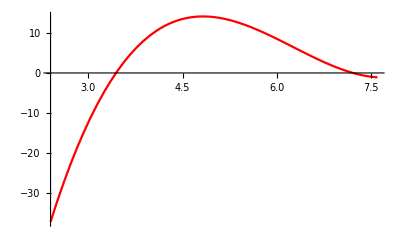

```mathematica
grL3 = Plot[L3[x], {x,2.4,7.6}, PlotStyle->Red]
```

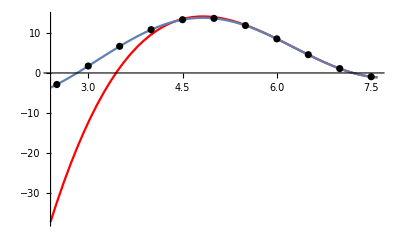

```mathematica
Show[grL3,grf,grp]
```

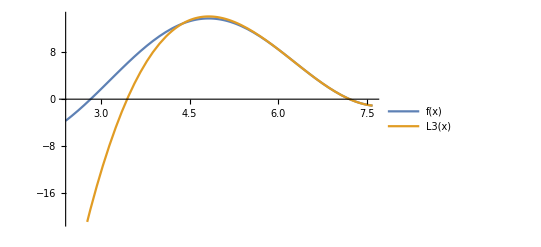

```mathematica
Plot[{f[x],L3[x]}, {x,2.4,7.6},PlotLegends->"Expressions"]
```

### Пресмятане приближена стойност на функцията в z = 6.85

```mathematica
L3[6.85]
```

2.02246

### Оценка на грешката

Истинска грешка

```mathematica
Abs[f[6.85]- L3[6.85]]
```

0.00498355

Теоретична грешка
Намираме М4

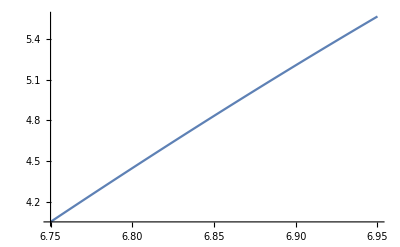

```mathematica
Plot[Abs[f''''[x]],{x, 6.75,6.95}]
```

От графиката се вижда, че

```mathematica
M4 = Abs[f''''[6.95]]
```

5.56638

```mathematica
R3[x_] := M4/(4!)* Abs[(x-(6))(x-(6.5))(x-(7))(x-(7.5))]
```

```mathematica
R3[6.85]
```

0.00672749

## Задача 2:

### а)

Дадена е системата линейни алгебрични уравнения

```mathematica
A=({{5+8+5, 0, 0, 0}, {-0, 10, 3, 0.5}, {3, 0, -8, -0}, {0.3, 0, 1.4, 12}}); b={5,1,-3,4*8};
(*инициализация на матрицата B и вектора c*)
n = Length[A];
c = Table[0,n];
B = Table[0,{i,n},{j,n}];
For[i = 1, i<=n, i++,
B[[i]] =- A[[i]]/A[[i,i]];
B[[i,i]]=0;
c[[i]]= b[[i]]/A[[i,i]]
]
Print["Итерационният процес е x^(k + 1) = ", B//MatrixForm, ". x^(k) + ", c//MatrixForm]
```

Итерационният процес е x^(k + 1) = (0 | 0 | 0 | 0
0 | 0 | -3/10 | -0.05
3/8 | 0 | 0 | 0
-0.025 | 0 | -0.116667 | 0). x^(k) + (5/18
1/10
3/8
8/3)

### б) Проверка условието на сходимост ||В|| < 1

#### Първа норма

```mathematica
n=Length[A]
```

4

```mathematica
Table[∑_(j=1)^n Abs[B[[i,j]]],{i,n}]
```

{0,0.35,3/8,0.141667}

```mathematica
Max[Table[∑_(j=1)^n Abs[B[[i,j]]],{i,n}]]
```

3/8

```mathematica
%//N
```

0.375

#### Втора норма

```mathematica
Table[∑_(i=1)^n Abs[B[[i,j]]],{j,n}]
```

{0.4,0,0.416667,0.05}

```mathematica
Max[Table[∑_(i=1)^n Abs[B[[i,j]]],{j,n}]]
```

0.416667

```mathematica
%//N
```

0.416667

#### Трета норма

```mathematica
√(∑_(i=1)^n ∑_(j=1)^n B[[i,j]]^2)
```

0.497354

```mathematica
%//N
```

0.497354

Избираме най малката възможна норма която в случая е втора
Следователно всеки избор на начално приближение е сходящ

### в) и г)

```mathematica
A=({{5+8+5, 0, 0, 0}, {-0, 10, 3, 0.5}, {3, 0, -8, -0}, {0.3, 0, 1.4, 12}}); b={5,1,-3,4*8};
(*инициализация на матрицата B и вектора c*)
n = Length[A];
c = Table[0,n];
B = Table[0,{i,n},{j,n}];
For[i = 1, i<=n, i++,
B[[i]] =- A[[i]]/A[[i,i]];
B[[i,i]]=0;
c[[i]]= b[[i]]/A[[i,i]]
]
Print["Итерационният процес е x^(k + 1) = ", B//MatrixForm, ". x^(k) + ", c//MatrixForm]

(*проверка на сходимост и избор на норма - отделно*)

x = {-10,0,0,10}; (*изборът на начално приближение е произволен*)
(*изчисляваме нормите според избора на норма, който сме направили по време на проверка на условието на устойчивост*)
normB = Max[Table[∑_(i=1)^n Abs[B[[i,j]]],{j,n}]]//N;
normx0 = Norm[x,1]//N;
normc = Norm[c,1]//N;
epszad = 10^-3;
eps=1;
For[k = 0, eps>epszad, k++,
Print["k = ", k, " x^(k) = ",x, " ε_k = ", eps = normB^k(normx0 +normc/(1-normB))//N];
x = B.x +c//N
]
Print["За сравнение, точното решение е ", LinearSolve[A,b]//N]
```

Итерационният процес е x^(k + 1) = (0 | 0 | 0 | 0
0 | 0 | -3/10 | -0.05
3/8 | 0 | 0 | 0
-0.025 | 0 | -0.116667 | 0). x^(k) + (5/18
1/10
3/8
8/3)

k = 0 x^(k) = {-10,0,0,10} ε_k = 25.8619

k = 1 x^(k) = {0.277778,-0.4,-3.375,2.91667} ε_k = 10.7758

k = 2 x^(k) = {0.277778,0.966667,0.479167,3.05347} ε_k = 4.48991

k = 3 x^(k) = {0.277778,-0.196424,0.479167,2.60382} ε_k = 1.8708

k = 4 x^(k) = {0.277778,-0.173941,0.479167,2.60382} ε_k = 0.779499

k = 5 x^(k) = {0.277778,-0.173941,0.479167,2.60382} ε_k = 0.324791

k = 6 x^(k) = {0.277778,-0.173941,0.479167,2.60382} ε_k = 0.13533

k = 7 x^(k) = {0.277778,-0.173941,0.479167,2.60382} ε_k = 0.0563874

k = 8 x^(k) = {0.277778,-0.173941,0.479167,2.60382} ε_k = 0.0234947

k = 9 x^(k) = {0.277778,-0.173941,0.479167,2.60382} ε_k = 0.00978947

k = 10 x^(k) = {0.277778,-0.173941,0.479167,2.60382} ε_k = 0.00407895

k = 11 x^(k) = {0.277778,-0.173941,0.479167,2.60382} ε_k = 0.00169956

k = 12 x^(k) = {0.277778,-0.173941,0.479167,2.60382} ε_k = 0.000708151

За сравнение, точното решение е {0.277778,-0.173941,0.479167,2.60382}

### Какъв е минималният брой итерации за достигане на точност 10^-7 при начално приближение х^(0) = (-10,0,10)

```mathematica
x = {-10,0,10}; epszad= 10^-7;
Log10[epszad/(normx0 +normc/(1-normB))]/Log10[normB]
```

22.1263

Извод: Необходими са 23 итерации за достигане на точност 10^-7 при приближение х^(0) = (-10,0,10)